```mathematica
Quit
```

## Load the package

```mathematica
PacletDirectoryLoad[FileNameJoin[{ParentDirectory@NotebookDirectory[],"packages"}]]
```

{/Users/christopher/git/ComputationalDiaries/packages}

```mathematica
Get["ComputationalDiaries`"]
```

## Import preassembled data

```mathematica
dataDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data"}]
```

/Users/christopher/git/ComputationalDiaries/data

```mathematica
grasshoffObservations=Import[FileNameJoin[{dataDirectory,"MX","grasshoffObservations.mx"}]];
jonesObservations=Import[FileNameJoin[{dataDirectory,"MX","jonesObservations.mx"}]];
```

## Basic analysis

Get the number of observations:

```mathematica
Length@grasshoffObservations
```

3484

```mathematica
Length@jonesObservations
```

1527

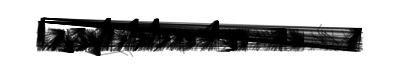

```mathematica
Graphics[{Opacity[0.3],Line[DeleteMissing[Function[obv,{
AstronomicalPosition[obv["ObjectA"],obv["Date"]],AstronomicalPosition[obv["ObjectB"],obv["Date"]]
}]/@Select[grasshoffObservations,#["Type"]==="RelativePosition"&],1,2]]},
PlotRange->{{0,360},{-15,15}},ImageSize->{Automatic,200}]
```

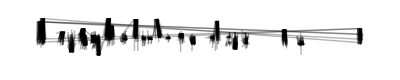

```mathematica
Graphics[{Opacity[0.3],Line[DeleteMissing[Function[obv,{
AstronomicalPosition[obv["ObjectA"],obv["Date"]],AstronomicalPosition[obv["ObjectB"],obv["Date"]]
}]/@Select[jonesObservations,#["Type"]==="RelativePosition"&],1,2]]},
PlotRange->{{0,360},{-15,15}},ImageSize->{Automatic,200}]
```

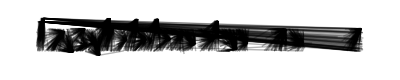

```mathematica
Graphics[{Opacity[0.3],Line[DeleteMissing[Function[obv,{
AstronomicalPosition[obv["ObjectA"],obv["Date"]],AstronomicalPosition[obv["ObjectB"],obv["Date"]]
}]/@Select[grasshoffObservations,#["Type"]==="RelativePosition"&&NormalStarQ[#["ObjectB"]]&],1,2]]},
PlotRange->{{0,360},{-15,15}},ImageSize->{Automatic,200}]
```

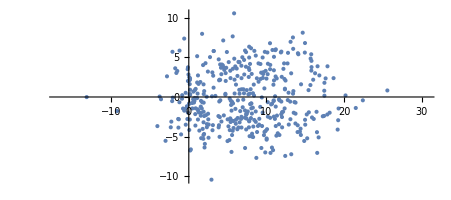

```mathematica
ListPlot[Function[obv,
AstronomicalPosition[obv["ObjectB"],obv["Date"]]-AstronomicalPosition[obv["ObjectA"],obv["Date"]]
]/@Select[grasshoffObservations,#["Type"]==="RelativePosition"&&!NormalStarQ[#["ObjectB"]]&],AspectRatio->Automatic]
```

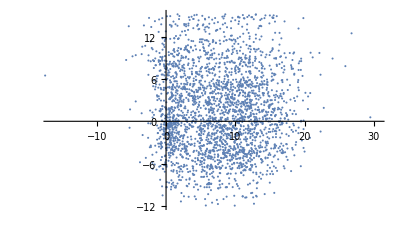

```mathematica
ListPlot[Function[obv,
AstronomicalPosition[obv["ObjectB"],obv["Date"]]-AstronomicalPosition[obv["ObjectA"],obv["Date"]]
]/@Select[grasshoffObservations,#["Type"]==="RelativePosition"&&NormalStarQ[#["ObjectB"]]&],AspectRatio->Automatic]
```

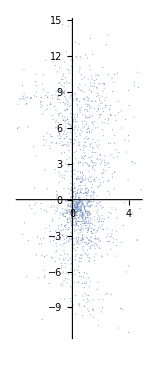

```mathematica
ListPlot[Function[obv,
AstronomicalPosition[obv["ObjectB"],obv["Date"]]-AstronomicalPosition[obv["ObjectA"],obv["Date"]]
]/@Select[jonesObservations,#["Type"]==="RelativePosition"&],AspectRatio->Automatic]
```

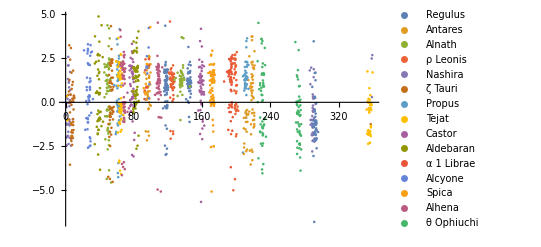

```mathematica
ListPlot[Merge[Function[obv,
obv["ObjectB"]->AstronomicalPosition[obv["ObjectA"],obv["Date"]]
]/@Select[jonesObservations,#["Type"]==="RelativePosition"&],Identity]]
```

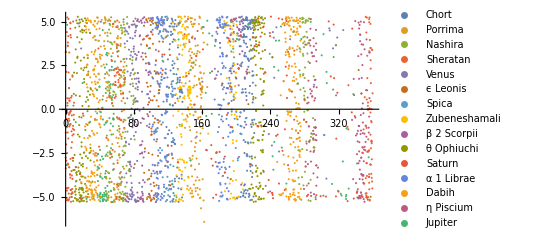

```mathematica
ListPlot[Merge[Function[obv,
obv["ObjectB"]->AstronomicalPosition[obv["ObjectA"],obv["Date"]]
]/@Select[grasshoffObservations,#["Type"]==="RelativePosition"&],Identity]]
```

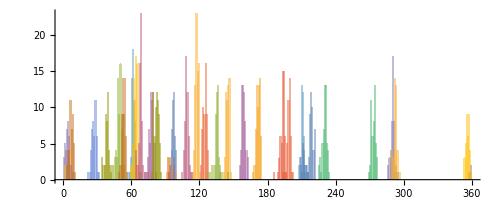

```mathematica
Histogram[KeyValueMap[Tooltip[#2,#1]&]@Merge[Function[obv,
obv["ObjectB"]->AstronomicalPosition[obv["ObjectA"],obv["Date"]][[1]]
]/@Select[jonesObservations,#["Type"]==="RelativePosition"&],Identity],{1},AspectRatio->Automatic]
```